2

```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

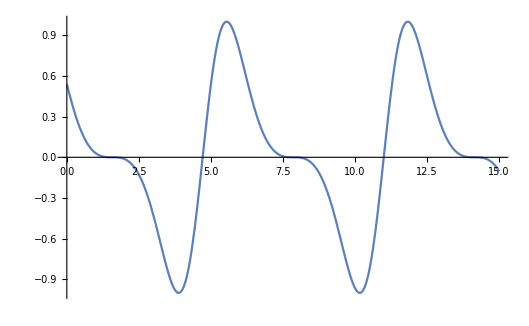

```mathematica
Plot[Cos[ x+Cos[ x]],{x,0,15}]
```

```mathematica
{a,b,c}.RotationMatrix[θ,{0,1,0}]
```

{a Cos[θ]-c Sin[θ],b,c Cos[θ]+a Sin[θ]}

```mathematica
ω1=0.3;
ω2=ω1/20;
ω3=-0.002;
angle =5.0;
anitropy=0;
B[{ω1_,ω2_,ω3_,angle_},t_,ind_]:={Cos[ω1 t]    Cos[ω2 t] ,Cos[ω1 t ] Sin[ ω2 t]  ,Sin[ ω1 t  +Cos[ω1 t]]  }.RotationMatrix[angle Degree*Boole[ind] ,{0,1,0}];

roller[ω1_,ω2_,ω3_,angle_,field_]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data1,data2,lm1,lm2


},
parameter={ω1,ω2,ω3,angle};
tMax = Min[200 2 π/parameter[[1]],50000.0]*0+4000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t ,field[[1]]     ]   ]];
(*force *)
F ={Sin[parameter[[4]] Degree] *anitropy*Boole[field[[2]]] ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}

]
```

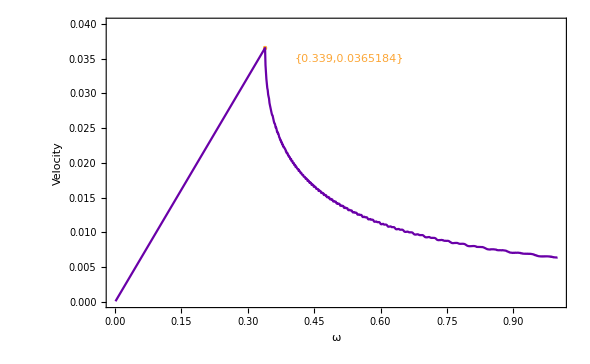

```mathematica
peak=FindPeaks[RollVelocity[[All,2]],Automatic,Automatic,0.03][[1,1]];

Show[ListPlot[{  RollVelocity[[peak]] },Epilog->{Text[Style[TraditionalForm[RollVelocity[[peak]] ],MPLColorMap["Plasma"][0.8],Medium],{0.53,0.035}]},
FrameStyle->Directive[Black,12],PlotRange->{{0,1},{0,0.04}},Frame->True,PlotStyle->{MPLColorMap["Plasma"][0.8],PointSize[Large]},FrameLabel->{ω,Velocity}

],
ListPlot[RollVelocity,Joined->True,PlotStyle->{MPLColorMap["Plasma"][0.2]}
]
]
```

```mathematica
ClearAll[phaseplot]
```

```mathematica
ω1=0.34;
ω2=ω1/10;
Timing[phaseplot=Table[{ω1,ω2,roller[ω1,ω2,0,10,{True, False}]},{ω1,0.33,0.37,0.002},{ω2,Table[ω1/k,{k,10.0,20.0,0.5}]}   ]; ]
```

```mathematica
phaseplot=Flatten[phaseplot,1];
phaseplot=ArrayReshape[phaseplot,{Length[phaseplot],4}];
```

```mathematica
Export[NotebookDirectory[]<>"phaseplot.csv",phaseplot]
```

/Users/yongdou/Desktop/magnetic roller/phaseplot.csv

```mathematica
phaseplot = ToExpression[Import[NotebookDirectory[]<>"phaseplot.csv"]];
phaseplot=ArrayReshape[phaseplot,{Length[phaseplot],4}];
```

/Users/yongdou/Dropbox/magnetic roller/

```mathematica
δx=phaseplot[[All,1;;3]];
δy=MapThread[Append,{phaseplot[[All,1;;2]],phaseplot[[All,4]]}];
```

```mathematica
MPLColorMap["Plasma"][1.183001729119405]
```

```mathematica
i=1;
While[i<(Length[δy[[All,3]]]+1),
 If[Abs[δy[[i,3]]]<0.06,δy[[i,3]]=0];
i++
]
```

```mathematica
1.37
```

```mathematica
Min[δy[[All,3]]]*1/1.37
```

-0.615848

```mathematica
Max[δy[[All,3]]]*1/1.37
```

0.387616

```mathematica
Export[NotebookDirectory[]<>"test.csv",test[[All,3]]]
```

/Users/yongdou/Desktop/magnetic roller/test.csv

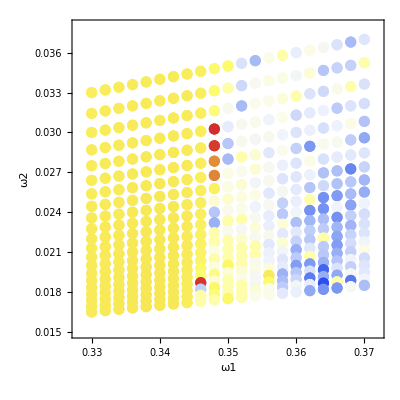

```mathematica
ListPlot[List/@δy[[All,1;;2]],PlotRange->{{0.328,0.372},{0.015,0.038}},PlotStyle->({PointSize[0.02],ColorData["TemperatureMap"][#/1.37+0.6]}&/@δy[[All,3]]),AspectRatio->1,Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"ω1","ω2"}]
```

```mathematica
DensityPlot[y,{x,0,1},{y,-10,10},ColorFunction->ColorData["TemperatureMap"],PlotRange->{{-10,10},{-10,10}},Frame->False,Axes->False]
```

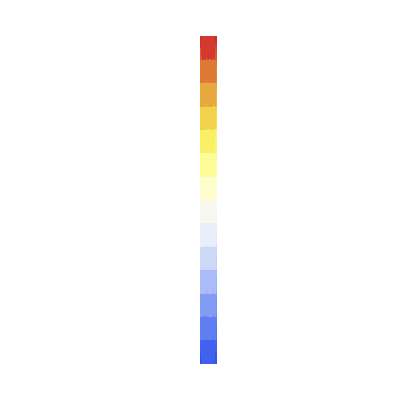

RGBColor[0.984192, 0.987731, 0.911643]

```mathematica
test=Table[     {ω1,ω2},{ω1,0.33,0.37,0.002},{ω2,Table[ω1/k,{k,10.0,20.0,0.5}]}    ];
Dimensions[test]
test=Flatten[test,1];
```

{21,21,2}

```mathematica
Dimensions[test]
```

{459,2}

```mathematica
0.37/0.007708333333333333
```

48.

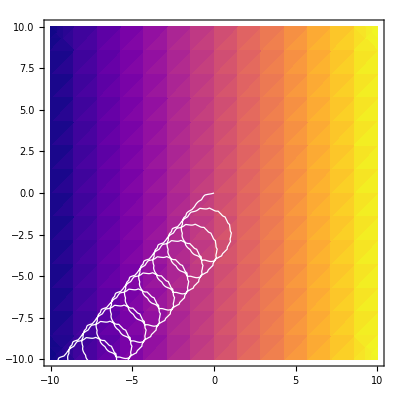

```mathematica
sol=roller[0.3,0.3/20,0,10,{True, False}][[1]];
Show[DensityPlot[x,{x,-10,10},{y,-10,10},ColorFunction->MPLColorMap["Plasma"],PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
ParametricPlot[{x[t]/.sol[[1]],y[t]/.sol[[1]]},{t,0,4000},PlotStyle->{White, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False]

]
```

```mathematica
data1=Table[{t/(  4 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(4π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
```

```mathematica
data1=Table[{t/(  4 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(4π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[   667  ]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      4 π/ω2]],x,x];
```

```mathematica
lm1
```

FittedModel[2.80606+0.064222 x]

```mathematica
3996 ,4000
```

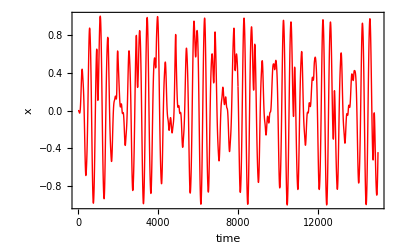

```mathematica
ListPlot[Table[q3[t]/.sol[[1]],{t,0,1500,0.1}],Joined->True,PlotStyle->{Red, Thick},Frame->True,Axes->False, Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"time","x"}]
```

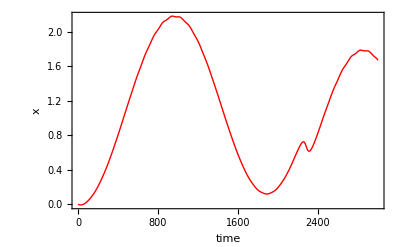

```mathematica
ListPlot[Table[x[t]/.sol[[1]],{t,0,300,0.1}],Joined->True,PlotStyle->{Red, Thick},Frame->True,Axes->False, Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"time","x"}]
```

```mathematica
season=Table[x[t]/.sol[[1]],{t,0,4000}];
```

```mathematica
2 π/ω2
```

418.879

```mathematica
Export["season.csv",season]
```

season.csv

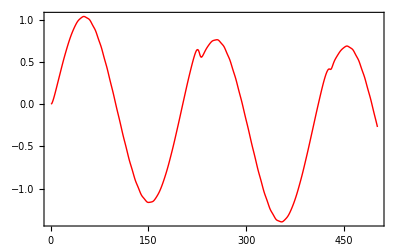

```mathematica
ListPlot[Table[y[t]/.sol[[1]],{t,0,500}],Joined->True,PlotStyle->{Red, Thick},Frame->True,Axes->False]
```

```mathematica
0.346/20
```

0.0173

```mathematica
eq1=HoldForm[{ω1=0.346,ω1=0.0173} ];

Rasterize[eq1//TraditionalForm,ImageSize->800]
```

-Graphics-

{0.-0.173648 Cos[0.3 t]+0.984808 Sin[0.03 t] Sin[0.3 t],0.+1. Cos[0.03 t] Sin[0.3 t],0.+0.984808 Cos[0.3 t]+0.173648 Sin[0.03 t] Sin[0.3 t]}

```mathematica
quaterionToRotationMatrix[{q0_,q1_,q2_,q3_}]:=Transpose[{{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}}];

R[t_]=quaterionToRotationMatrix[{q0[t],q1[t],q2[t],q3[t]}/.sol[[1]]];
```

```mathematica
R[0.2]
```

{{0.999935,0.0000255511,-0.011376},{8.59712×10^-7,0.999997,0.00232162},{0.011376,-0.00232148,0.999933}}

```mathematica
e1[t_]:=R[t].{1,0,0}; (* Body axes in the space frame are rotating *)
e2[t_]:=R[t].{0,1,0};
e3[t_]:=R[t].{0,0,1};
```

```mathematica
PlotRotate[tt_]:=
Graphics3D[{

{Red,Tube[{{0,0,0},e1[tt]},0.015]},
{Red,Sphere[e1[tt],0.1]}, (* e1 axis has a red sphere, rotating *)
{Green,Tube[{{0,0,0},e2[tt]},0.015]},
{Green,Sphere[e2[tt],0.1]}, (* e2 axis has a green sphere, rotating *) 
{Blue,Tube[{{0,0,0},e3[tt]},0.015]},
{Blue,Sphere[e3[tt],0.1]}, (* e3 axis has a blue sphere, rotating *)
{Red,Arrow[Tube[{{0,0,0},{1,0,0}}]]}, (* x-axis is red, fixed *)
{Green,Arrow[Tube[{{0,0,0},{0,1,0}}]]}, (* y-axis is green, fixed *)
{Blue,Arrow[Tube[{{0,0,0},{0,0,1}}]]}},(* z-axis is blue, fixed *)
PlotRange->1.5,ViewPoint->{1,1,1.5},ImageSize->395]
```

```mathematica
(*Animate[
PlotRotate[t],
{{t,190,"time"},190,300,AnimationRate->5,Appearance->"Labeled",ImageSize->Tiny}]*)
```

```mathematica
racher
```

```mathematica
sin(𝑥+1 2 sin(𝑥))
```

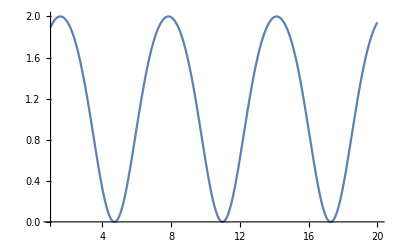

```mathematica
Plot[Sin[x+0.2Cos[x]]+1,{x,1,20}]
```

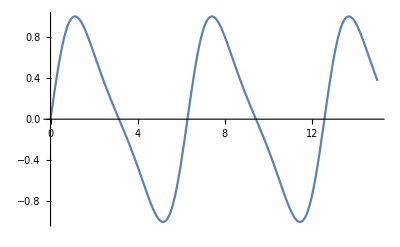

```mathematica
Plot[Sin[x+0.5 Sin[x]],{x,0,15}]
```

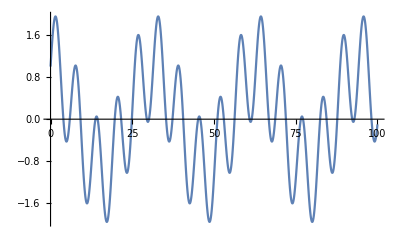

```mathematica
Plot[Sin[x]+Cos[0.2 x],{x,0,100}]
```

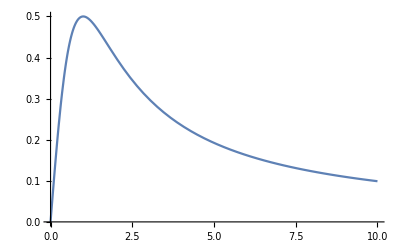

```mathematica
Plot[x/(1+x^2),{x,0,10}]
```